```mathematica
<<MaTeX`
```

```mathematica
(* markers for plotting *)
markerCirc = Graphics[{#, EdgeForm[{#}], FaceForm[Opacity[.075]], Disk[]}]&;
markerDisk = Graphics[{#,  EdgeForm[{#}], FaceForm[Opacity[0.7]], Disk[]}]&;
markerTriangle =  Graphics[{#,  EdgeForm[{#}], FaceForm[Opacity[.7]], Triangle[{{0,0},{0.5, (√3)/2},{1,0}}]}]&;
(* markers examples *)
GraphicsRow[{ markerCirc[Gray],markerDisk[Gray], markerTriangle[Gray] }, ImageSize->100]
(* color for train/test points *)
testpntsCol= RGBColor[0.07,0.66,1];
trainpntsCol = RGBColor[1,0.36,0.08];
```

-Graphics-

```mathematica
(* training / test points *)
trainPoints = {0.1->0.5, 0.2 ->0.2, 0.4->0.1, 0.5->0.25, 0.8->0.47,0.9->0.48, 1-> 0.5};
testPoints = {0.3, 0.7};
```

```mathematica
(* fit GP *)
gp=Predict[trainPoints,Method->"GaussianProcess"]
```

PredictorFunction[…]

```mathematica
maxy = 1;
lines=Line[{{#,-maxy},{#,maxy}}]&/@testPoints;
lineStyle = {Red, Dashed};
```

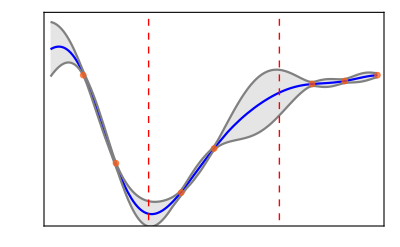

```mathematica
xTicks={0,  0.2,  0.4, 0.6,  0.8, 1};
yTicks = {0,  0.2, 0.4, 0.6};
plot = Show[
Plot[{gp[x],gp[x]+StandardDeviation[gp[x, "Distribution"]], gp[x]-StandardDeviation[gp[x, "Distribution"]]}, {x, 0, 1}, 
PlotStyle->{Blue, Gray, Gray},
Filling->{2->{3}},
Exclusions->False,
PerformanceGoal->"Speed"
],
ListPlot[List@@@trainPoints,  PlotMarkers->{markerDisk[trainpntsCol], 0.05}],
Frame->True,
FrameTicks->{{{#, MaTeX[#,Magnification->1.5]}&/@yTicks, None}, {{#, MaTeX[#,Magnification->1.5]}&/@xTicks, None}},
FrameLabel->{MaTeX["x", Magnification->1.5], MaTeX["y", Magnification->1.5](*,MaTeX["\\text{Test data}", Magnification->1.5]*)},
PlotRange->{{0, 1},{0, 0.7}},
Epilog->{Directive[lineStyle], lines},
PlotRangePadding->0.05
]
```

```mathematica
Export[NotebookDirectory[]<>"imgs/regress.svg", plot]
```

/home/denys/Documents/ifw/ml/datasciencesnippets/gpr/imgs/regress.svg